```mathematica
模拟随机力,观察随机运动
```

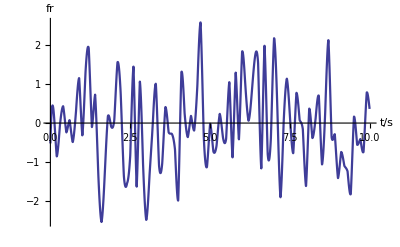

NDSolve::dsvar: {{0.01, 3.2477857566265193664227192046×10^-12}, {0.01005, 3.2727580149717039559212560695×10^-12}, « 48 », « 26751 »} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: {{0.01, 3.24779×10^-12}, {0.01005, 3.27276×10^-12}, {0.0101, 3.29784×10^-12}, {0.01015, 3.32304×10^-12}, « 44 », {0.0124, 4.58171×10^-12}, {0.01245, 4.61264×10^-12}, « 26751 »} cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: {{0.01, 3.24779×10^-12}, {0.01005, 3.27276×10^-12}, {0.0101, 3.29784×10^-12}, {0.01015, 3.32304×10^-12}, « 44 », {0.0124, 4.58171×10^-12}, {0.01245, 4.61264×10^-12}, « 26751 »} cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
dis=NormalDistribution[0,1];
m=1000;  δt=0.1;  time=(m-1)*δt;α=0.7;      
fr=Table[RandomReal[dis],{m}];
fr=Table[{δt*(j-1),fr[[j]]},{j,m}];   
fr=Interpolation[fr];  
Plot[fr[t],{t,0,time/10},AxesLabel->{"t/s","fr"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]     
equ={x''[t]+α*x'[t]==fr[t],x[0]==0,x'[0]==0};   
s=NDSolve[equ,x,{t,0,time},MaxSteps->∞];
Plot[x[t]/.s,{t,0,time},AxesLabel->{"t/s","x"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[dis,m,δt,time,α,fr,s,x,equ]
```